# Impulsive waves in de Sitter and anti - de Sitter space - times generated by null particles with an arbitrary multipole structure by Podolsky and Griffiths

Geoff Cope	
University of Utah
February 14th, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article

```mathematica
Hyperlink["Impulsive waves in de Sitter and anti - de Sitter space - times generated by null particles with an arbitrary multipole structure by Podolsky and Griffiths",
"https://arxiv.org/abs/gr-qc/9710049"]
```

[Impulsive waves in de Sitter and anti - de Sitter space - times generated by null particles with an arbitrary multipole structure by Podolsky and Griffiths](https://arxiv.org/abs/gr-qc/9710049)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 252 Kb

{Utilities`CleanSlate`,Notation`,GeneralRelativityTensors`,SpinWeightedSpheroidalHarmonics`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Palette and Notation

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[Z, 0]]
Symbolize[Subscript[Z, 1]]
Symbolize[Subscript[Z, 2]]
Symbolize[Subscript[Z, 3]]
Symbolize[Subscript[Z, 4]]
Symbolize[Subscript[η, 0]]
Symbolize[Subscript[t, 0]]
Symbolize[Subscript[t, -1]]
Symbolize[Subscript[t, b]]
Symbolize[Subscript[z, b]]
Symbolize[Subscript[t, k]]
Symbolize[Subscript[z, k]]
```

```mathematica
CreatePalette[{ 
PasteButton[Subscript[Z, 0]],
 PasteButton[Subscript[Z, 1]] , 
PasteButton[Subscript[Z, 2]] ,
PasteButton[Subscript[Z, 3]] ,
PasteButton[Subscript[Z, 4]] ,
PasteButton[Subscript[η, 0]] ,
PasteButton[Subscript[t, 0]] ,
PasteButton[Subscript[t, -1]] ,
PasteButton[Subscript[t, b]] ,
PasteButton[Subscript[z, b]] ,
PasteButton[Subscript[t, k]] ,
PasteButton[Subscript[z, k]]
}
]
```

qpith_shm111FrontEndObject[LinkObject["qpith_shm", 3, 1]]111Untitled-9

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[Subscript[Z, 0]] -> Subscript[dZ, 0] ,
Dt[Subscript[Z, 1]] -> Subscript[dZ, 1] ,
Dt[Subscript[Z, 2]]-> Subscript[dZ, 2] ,
Dt[Subscript[Z, 3]]-> Subscript[dZ, 3] ,
Dt[Subscript[Z, 4]] -> Subscript[dZ, 4] ,
 Dt[Subscript[η, 0]]-> Subscript[dη, 0] , 
 Dt[Subscript[t, 0]]-> Subscript[dt, 0] , 
 Dt[t]-> dt ,
 Dt[T]-> dT ,
Dt[χ] -> dχ , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  ,
Dt[R] -> dR  ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz  ,
Dt[Subscript[t, -1]]-> Subscript[dt, -1] , 
Dt[Subscript[t, b]]-> Subscript[dt, b] ,
Dt[Subscript[z, b]]-> Subscript[dz, b] ,
Dt[Subscript[t, k]] -> Subscript[dt, k] ,
Dt[Subscript[z, k]] -> Subscript[dz, k] , 
Dt[ρ] -> dρ 
} ;
dtReplace // TableForm
```

Dt[Z_0]→dZ_0
Dt[Z_1]→dZ_1
Dt[Z_2]→dZ_2
Dt[Z_3]→dZ_3
Dt[Z_4]→dZ_4
Dt[η_0]→dη_0
Dt[t_0]→dt_0
Dt[t]→dt
Dt[T]→dT
Dt[χ]→dχ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[R]→dR
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[t_-1]→dt_-1
Dt[t_b]→dt_b
Dt[z_b]→dz_b
Dt[t_k]→dt_k
Dt[z_k]→dz_k
Dt[ρ]→dρ

```mathematica
a/:Dt[a]=0  ;
Λ/:Dt[Λ]=0  ;
ϵ/:Dt[ϵ]=0  ;
(* Differential of a is zero , a is a constant , etc.  *)
```

```mathematica
Clear[lineTometric]
lineTometric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

## Line Element and Metric 3

```mathematica
Clear[eq1]  
eq1 = 
 Subscript[Z, 0]^2- Subscript[Z, 1]^2-Subscript[Z, 2]^2-Subscript[Z, 3]^2- ϵ Subscript[Z, 4]^2==-ϵ a^2   (* /. a->√(3/(ϵ Λ))  *)  (* /. ϵ-> 1 for de Sitter  /. ϵ-> -1 for AdS *)
```

Z_0^2-Z_1^2-Z_2^2-Z_3^2-Z_4^2 ϵ==-a^2 ϵ

```mathematica
Clear[eq1a]
eq1a = 
 - Subscript[dZ, 0]^2 + Subscript[dZ, 1]^2+ Subscript[dZ, 2]^2+Subscript[dZ, 3]^2+ ϵ Subscript[dZ, 4]^2
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+ϵ dZ_4^2

```mathematica
Clear[eq2]
eq2 = {
Subscript[Z, 0]+Subscript[Z, 1]== 0 , 
Subscript[Z, 2]^2+ Subscript[Z, 3]^2+ ϵ Subscript[Z, 4]^2== ϵ a^2
} ;
eq2 // TableForm
```

Z_0+Z_1==0
Z_2^2+Z_3^2+Z_4^2 ϵ==a^2 ϵ

```mathematica
Clear[δ]
δ[u_]:= DiracDelta[u]
```

```mathematica
Clear[eq3]
eq3 = 
Subscript[dZ, 0]^2- Subscript[dZ, 1]^2-Subscript[dZ, 2]^2-Subscript[dZ, 3]^2- ϵ Subscript[dZ, 4]^2- H[Subscript[Z, 2],Subscript[Z, 3],Subscript[Z, 4]] δ[Subscript[Z, 0]+Subscript[Z, 1]] ( Subscript[dZ, 0]+Subscript[dZ, 1])^2
```

dZ_0^2-dZ_1^2-DiracDelta[Z_0+Z_1] H[Z_2,Z_3,Z_4] (dZ_0+dZ_1)^2-dZ_2^2-dZ_3^2-ϵ dZ_4^2

```mathematica
Clear[eq4]
eq4 = {
Subscript[Z, 2]== a √(ϵ(1-z^2))Cos[ϕ] , 
Subscript[Z, 3]== a √(ϵ(1-z^2))Sin[ϕ] , 
Subscript[Z, 4]== a z
} ;
eq4  // TableForm
```

Z_2==a √((1-z^2) ϵ) Cos[ϕ]
Z_3==a √((1-z^2) ϵ) Sin[ϕ]
Z_4==a z

```mathematica
Dt[ eq4 ] /. dtReplace  /. Equal-> Rule  // TableForm
```

dZ_2→-(a dz z ϵ Cos[ϕ])/(√((1-z^2) ϵ))-a dϕ √((1-z^2) ϵ) Sin[ϕ]
dZ_3→a dϕ √((1-z^2) ϵ) Cos[ϕ]-(a dz z ϵ Sin[ϕ])/(√((1-z^2) ϵ))
dZ_4→a dz

```mathematica
Collect[ (eq3 /. ( Dt[ eq4 ] /. dtReplace /. Equal-> Rule  ) // Expand // Simplify) , {Subscript[dZ, 0]^2, Subscript[dZ, 1]^2, dz^2, dϕ^2}]  /. H[Subscript[Z, 2],Subscript[Z, 3],Subscript[Z, 4]]-> H[z,ϕ]
```

(a^2 dz^2 ϵ)/(-1+z^2)+a^2 dϕ^2 (-1+z^2) ϵ+(1-DiracDelta[Z_0+Z_1] H[z,ϕ]) dZ_0^2-2 DiracDelta[Z_0+Z_1] H[z,ϕ] dZ_0 dZ_1+(-1-DiracDelta[Z_0+Z_1] H[z,ϕ]) dZ_1^2

```mathematica
Clear[metric3]
metric3 = 
lineTometric[
Collect[ (eq3 /. ( Dt[ eq4 ] /. dtReplace /. Equal-> Rule  ) // Expand // Simplify) , {Subscript[dZ, 0]^2, Subscript[dZ, 1]^2, dz^2, dϕ^2}]/. H[Subscript[Z, 2],Subscript[Z, 3],Subscript[Z, 4]]-> H[z,ϕ]   , { dz,dϕ,Subscript[dZ, 0],Subscript[dZ, 1]}]  ;
metric3// MatrixForm
```

((a^2 ϵ)/(-1+z^2) | 0 | 0 | 0
0 | a^2 (-1+z^2) ϵ | 0 | 0
0 | 0 | 1-DiracDelta[Z_0+Z_1] H[z,ϕ] | -DiracDelta[Z_0+Z_1] H[z,ϕ]
0 | 0 | -DiracDelta[Z_0+Z_1] H[z,ϕ] | -1-DiracDelta[Z_0+Z_1] H[z,ϕ])

```mathematica
Clear[inverse3]
inverse3 = 
Inverse[ metric3 ] // Expand // Simplify ;
inverse3 // MatrixForm
```

```mathematica
metric3 . inverse3 // Expand // Simplify // MatrixForm
```

```mathematica
inverse3 . metric3  // Expand // Simplify // MatrixForm
```

## Tensors Calculated For Metric 3

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;  
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last Timing took 32.33 for all tensors *) 
input[ "metric3", metric3, "Impulsive","g^Impuslive",{z,ϕ,Subscript[Z, 0],Subscript[Z, 1]}, "Greek"] // Timing
```

{32.3339,Null}

```mathematica
tensorList
```

{(g^Impuslive)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm
```

(g^Impuslive)_αβ^

Impulsive

((a^2 ϵ)/(-1+z^2) | 0 | 0 | 0
0 | a^2 (-1+z^2) ϵ | 0 | 0
0 | 0 | 1-DiracDelta[Z_0+Z_1] H[z,ϕ] | -DiracDelta[Z_0+Z_1] H[z,ϕ]
0 | 0 | -DiracDelta[Z_0+Z_1] H[z,ϕ] | -1-DiracDelta[Z_0+Z_1] H[z,ϕ])

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]]  // Expand // Simplify // MatrixForm
```

Γ_βγ^α

ChristoffelSymbolImpulsive

((-z/(-1+z^2)
0
0
0) | (0
z-z^3
0
0) | (0
0
-(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ)
-(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ)) | (0
0
-(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ)
-(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ))
(0
z/(-1+z^2)
0
0) | (z/(-1+z^2)
0
0
0) | (0
0
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)) | (0
0
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ))
(0
0
-1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
-1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]) | (0
0
-1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]
-1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]) | (-1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
-1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]
-1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1]
-1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1]) | (-1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
-1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]
-1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1]
-1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1])
(0
0
1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]) | (0
0
1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]
1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]) | (1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]
1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1]
1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1]) | (1/2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
1/2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ]
1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1]
1/2 H[z,ϕ] DiracDelta'[Z_0+Z_1]))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // Expand // Simplify // MatrixForm
```

R_αβγδ^

RiemannTensorImpulsive

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -a^2 ϵ | 0 | 0
a^2 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ]
0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0) | (0 | 0 | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ]
0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0)
(0 | a^2 ϵ | 0 | 0
-a^2 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
0 | 0 | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0) | (0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
0 | 0 | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0)
(0 | 0 | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ]
0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0) | (0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
0 | 0 | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2-2 z^2)-1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ]
0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 (-1+z^2))+1/2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 0 | 0) | (0 | 0 | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | (z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 (-1+z^2))-1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ]
0 | 0 | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | -1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]+1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]-1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0
(z DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2-2 z^2)+1/2 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ] | 1/2 DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ]-1/2 z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ]+1/2 z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ] | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]]  // Expand // Simplify // MatrixForm
```

R_βγ^

RicciTensorImpulsive

(1/(1-z^2) | 0 | 0 | 0
0 | 1-z^2 | 0 | 0
0 | 0 | (DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ) | (DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)
0 | 0 | (DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ) | (DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ))

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]]  // Expand // Simplify
```

R

RicciScalarImpulsive

-2/(a^2 ϵ)

```mathematica
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]]  // Expand // Simplify
```

K

KretschmannScalarImpulsive

4/(a^4 ϵ^2)

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]]  // Expand // Simplify // MatrixForm
```

G_αβ^

EinsteinTensorImpulsive

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/(a^2 ϵ)+(DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 ϵ-a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ) | (DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 ϵ-a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)
0 | 0 | (DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 ϵ-a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ) | -1/(a^2 ϵ)+(DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H[z,ϕ])/(a^2 ϵ-a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(2 a^2 ϵ))

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]]  // Expand // Simplify // MatrixForm
```

C_αβγδ^

WeylTensorImpulsive

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(a^2 ϵ)/3 | 0 | 0
(a^2 ϵ)/3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1) | (1)
(0 | (a^2 ϵ)/3 | 0 | 0
-(a^2 ϵ)/3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1) | (1)
(1) | (1) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/(3 a^2 ϵ)
0 | 0 | -1/(3 a^2 ϵ) | 0)
(1) | (1) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/(3 a^2 ϵ)
0 | 0 | 1/(3 a^2 ϵ) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))
 |  |  |  |

```mathematica
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]]  // Expand // Simplify // MatrixForm
```

C_αβγ^

CottonTensorImpulsive

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)-(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(5 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)
(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)-(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(5 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)) | (0
0
(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)
(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)) | (-(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 ϵ-3 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(3 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)
0
0) | (-(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 ϵ-3 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(3 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)
0
0)
(0
0
(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)-(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(5 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)
(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)-(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(5 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)) | (0
0
(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)
(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)-(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)) | (-(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 ϵ-3 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(3 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)
0
0) | (-(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z^3 DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 (-1+z^2)^2 ϵ)+(2 z DiracDelta[Z_0+Z_1] H[z,ϕ])/(3 a^2 ϵ-3 a^2 z^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(0,2)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(2 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)-(2 z^4 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2)^2 ϵ)+(3 z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(1,0)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(1,2)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 ϵ)-(z DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(2,0)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(3,0)[z,ϕ])/(2 a^2 ϵ)
(DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(0,1)[z,ϕ])/(2 a^2 ϵ-2 a^2 z^2 ϵ)+(DiracDelta[Z_0+Z_1] H^(0,3)[z,ϕ])/(2 a^2 (-1+z^2) ϵ)-(z DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)+(z^3 DiracDelta[Z_0+Z_1] H^(1,1)[z,ϕ])/(a^2 (-1+z^2) ϵ)-(DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)+(z^2 DiracDelta[Z_0+Z_1] H^(2,1)[z,ϕ])/(2 a^2 ϵ)
0
0))

```mathematica
Clear[nonzeroRicci]
nonzeroRicci = { 
TensorValues[tensorList[[4]]][[1,1]] // Expand // Simplify  , 
     TensorValues[tensorList[[4]]][[2,2]] // Expand // Simplify  , 
     Collect[(2 a^2 ϵ)*TensorValues[tensorList[[4]]][[3,3]] // Expand // Simplify  , { Derivative[2,0][H][z,ϕ] , Derivative[0,2][H][z,ϕ], Derivative[1,0][H][z,ϕ]}] , 
     Collect[(2 a^2 ϵ)* TensorValues[tensorList[[4]]][[3,4]]  // Expand // Simplify ,  { Derivative[2,0][H][z,ϕ] , Derivative[0,2][H][z,ϕ], Derivative[1,0][H][z,ϕ]}] , 
     Collect[(2 a^2 ϵ)* TensorValues[tensorList[[4]]][[4,4]] // Expand // Simplify  ,  { Derivative[2,0][H][z,ϕ] , Derivative[0,2][H][z,ϕ], Derivative[1,0][H][z,ϕ]}]
} ;
nonzeroRicci  /. δ[Subscript[Z, 0]+Subscript[Z, 1]]-> 1  // TableForm
```

1/(1-z^2)
1-z^2
(H^(0,2)[z,ϕ])/(-1+z^2)+(-(2 z)/(-1+z^2)+(2 z^3)/(-1+z^2)) H^(1,0)[z,ϕ]+(-1+z^2) H^(2,0)[z,ϕ]
(H^(0,2)[z,ϕ])/(-1+z^2)+(-(2 z)/(-1+z^2)+(2 z^3)/(-1+z^2)) H^(1,0)[z,ϕ]+(-1+z^2) H^(2,0)[z,ϕ]
(H^(0,2)[z,ϕ])/(-1+z^2)+(-(2 z)/(-1+z^2)+(2 z^3)/(-1+z^2)) H^(1,0)[z,ϕ]+(-1+z^2) H^(2,0)[z,ϕ]

```mathematica
(-1)*( nonzeroRicci[[3]]   /. δ[Subscript[Z, 0]+Subscript[Z, 1]]-> 1   // Simplify )  // Expand // Simplify  // pdConv
(-1)*( nonzeroRicci[[4]]   /. δ[Subscript[Z, 0]+Subscript[Z, 1]]-> 1   // Simplify )  // Expand // Simplify  // pdConv
(-1)*( nonzeroRicci[[5]]   /. δ[Subscript[Z, 0]+Subscript[Z, 1]]-> 1   // Simplify )  // Expand // Simplify
```

-((∂^2 H(z,ϕ))/(∂ϕ^2))/(z^2-1)-(z^2-1) (∂^2 H(z,ϕ))/(∂z^2)-2 z (∂H(z,ϕ))/(∂z)

-((∂^2 H(z,ϕ))/(∂ϕ^2))/(z^2-1)-(z^2-1) (∂^2 H(z,ϕ))/(∂z^2)-2 z (∂H(z,ϕ))/(∂z)

-(H^(0,2)[z,ϕ])/(-1+z^2)-2 z H^(1,0)[z,ϕ]-(-1+z^2) H^(2,0)[z,ϕ]

```mathematica
Clear[eq5a] (* IMPORTANT!!! MISSING 2 H Term on LHS *) 
eq5a = 
((-1)*( nonzeroRicci[[5]]   /. δ[Subscript[Z, 0]+Subscript[Z, 1]]-> 1   // Simplify )  // Expand // Simplify )== 0  ;
eq5a // pdConv
```

-((∂^2 H(z,ϕ))/(∂ϕ^2))/(z^2-1)-(z^2-1) (∂^2 H(z,ϕ))/(∂z^2)-2 z (∂H(z,ϕ))/(∂z)==0

```mathematica
(* Just typing in correct form without deriving... *) 
Clear[eq5]
eq5 = 
((-1)*( nonzeroRicci[[5]]   /. δ[Subscript[Z, 0]+Subscript[Z, 1]]-> 1   // Simplify )  // Expand // Simplify  ) +(*added by hand until done properly*) 2 H[z,ϕ]
```

2 H[z,ϕ]-(H^(0,2)[z,ϕ])/(-1+z^2)-2 z H^(1,0)[z,ϕ]-(-1+z^2) H^(2,0)[z,ϕ]

```mathematica
eq5 // pdConv
```

-((∂^2 H(z,ϕ))/(∂ϕ^2))/(z^2-1)-(z^2-1) (∂^2 H(z,ϕ))/(∂z^2)+2 H(z,ϕ)-2 z (∂H(z,ϕ))/(∂z)

```mathematica
Clear[seperationOfVars]
seperationOfVars = 
H[z,ϕ] -> h[z] Exp[ⅈ m ϕ]
```

H[z,ϕ]→ⅇ^(ⅈ m ϕ) h[z]

```mathematica
D[seperationOfVars, z] // pdConv
D[D[seperationOfVars, z], z] // pdConv
D[D[seperationOfVars, ϕ], ϕ] // pdConv
```

(∂H(z,ϕ))/(∂z)→ⅇ^(ⅈ m ϕ) (∂h(z))/(∂z)

(∂^2 H(z,ϕ))/(∂z^2)→ⅇ^(ⅈ m ϕ) (∂^2 h(z))/(∂z^2)

(∂^2 H(z,ϕ))/(∂ϕ^2)→m^2 h(z) (-ⅇ^(ⅈ m ϕ))

```mathematica
eq5  /. seperationOfVars /. D[seperationOfVars, z]  /. D[D[seperationOfVars, z], z]   /. D[D[seperationOfVars, ϕ], ϕ]
```

2 ⅇ^(ⅈ m ϕ) h[z]+(ⅇ^(ⅈ m ϕ) m^2 h[z])/(-1+z^2)-2 ⅇ^(ⅈ m ϕ) z h'[z]-ⅇ^(ⅈ m ϕ) (-1+z^2) h''[z]

```mathematica
Clear[intermediateSOV]
intermediateSOV = 
(1/H[z,ϕ]/. seperationOfVars)*(eq5  /. seperationOfVars /. D[seperationOfVars, z]  /. D[D[seperationOfVars, z], z]   /. D[D[seperationOfVars, ϕ], ϕ] ) // Expand // Simplify
```

2+m^2/(-1+z^2)-(2 z h'[z]+(-1+z^2) h''[z])/h[z]

```mathematica
Clear[intermediateSOVa]
intermediateSOVa = 
Collect[ Together[intermediateSOV][[3]] , {h''[z] , h'[z] , h[z] } ]
```

(-2+m^2+2 z^2) h[z]+(2 z-2 z^3) h'[z]+(-1+2 z^2-z^4) h''[z]

```mathematica
Clear[eq6] (* equivalent but looks different because of grouping on h[z] *) 
eq6 = 
(1/(-1+z^2))*Sum[Simplify[intermediateSOVa [[i]]] , {i,1, Length[ intermediateSOVa]}] // Expand // Simplify
```

((-2+m^2+2 z^2) h[z])/(-1+z^2)-2 z h'[z]-(-1+z^2) h''[z]

```mathematica
Clear[eq6a]
eq6a = 
Flatten[DSolve[ eq6  == 0  , h[z],z]] /. C[1]-> a[m] /. C[2]-> b[m]
```

{h[z]→a[m] LegendreP[1,m,z]+b[m] LegendreQ[1,m,z]}


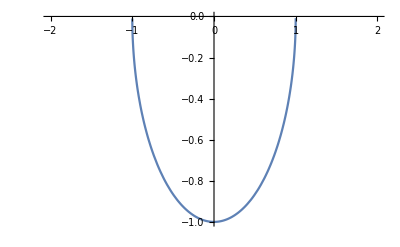
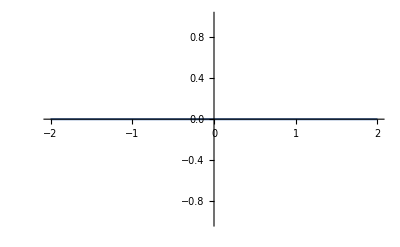
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Nonzero only for m = 0, 1 *) 
Table[Plot[  LegendreP[1,m,z]  , {z,-2,2}] , {m,0,5}]
```

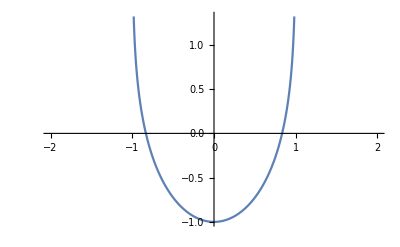
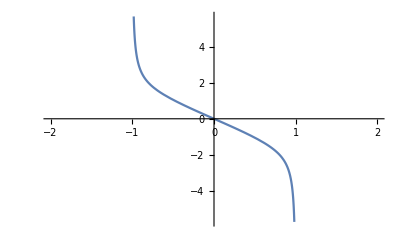
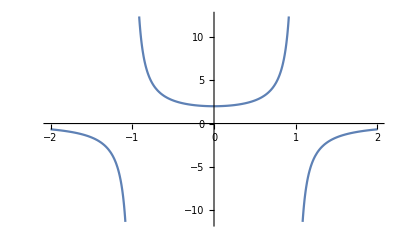
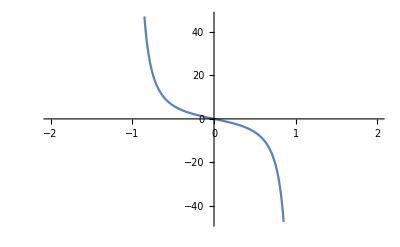
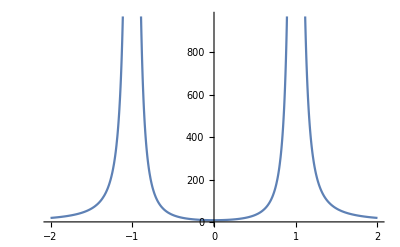
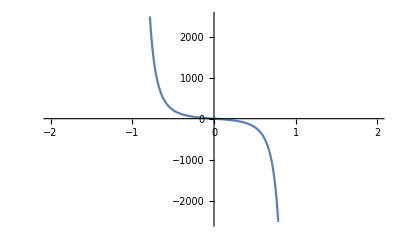

```mathematica
(* Singular at z = 1,-1 *) 
Table[Plot[  LegendreQ[1,m,z]  , {z,-2,2}] , {m,0,5}]
```

```mathematica
Clear[eq8]
eq8 = 
Table[LegendreQ[1,m,z] , {m,0,3}]  ;
eq8 //Simplify //  TableForm
```

1/2 (-2-z Log[1-z]+z Log[1+z])
-(2 z+(-1+z^2) Log[1-z]-(-1+z^2) Log[1+z])/(2 √(1-z^2))
-2/(-1+z^2)
-(8 z)/((1-z^2)^(3/2))

```mathematica
Clear[eq10]
eq10 = {
Subscript[Z, 0] == -a Cot[η] , 
Subscript[Z, 1]== a Csc[η]Cos[χ] , 
Subscript[Z, 2]== a Csc[η] Sin[χ] Sin[θ] Cos[ϕ] , 
Subscript[Z, 3]== a Csc[η]Sin[χ] Sin[θ] Sin[ϕ] , 
Subscript[Z, 4]== a Csc[η] Sin[χ] Cos[θ] 
} ;
eq10  // TableForm
```

Z_0==-a Cot[η]
Z_1==a Cos[χ] Csc[η]
Z_2==a Cos[ϕ] Csc[η] Sin[θ] Sin[χ]
Z_3==a Csc[η] Sin[θ] Sin[ϕ] Sin[χ]
Z_4==a Cos[θ] Csc[η] Sin[χ]

```mathematica
eq1/. ϵ-> 1 
eq1/. ϵ-> 1 /.( eq10  /. Equal-> Rule )
eq1 /. ϵ-> 1 /.( eq10  /. Equal-> Rule ) // Expand // Simplify
```

Z_0^2-Z_1^2-Z_2^2-Z_3^2-Z_4^2==-a^2

a^2 Cot[η]^2-a^2 Cos[χ]^2 Csc[η]^2-a^2 Cos[θ]^2 Csc[η]^2 Sin[χ]^2-a^2 Cos[ϕ]^2 Csc[η]^2 Sin[θ]^2 Sin[χ]^2-a^2 Csc[η]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[χ]^2==-a^2

True

```mathematica
Dt[ eq10 ] /. dtReplace  /. Equal-> Rule  // TableForm
```

dZ_0→a dη Csc[η]^2
dZ_1→-a dη Cos[χ] Cot[η] Csc[η]-a dχ Csc[η] Sin[χ]
dZ_2→a dχ Cos[ϕ] Cos[χ] Csc[η] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Csc[η] Sin[χ]-a dη Cos[ϕ] Cot[η] Csc[η] Sin[θ] Sin[χ]-a dϕ Csc[η] Sin[θ] Sin[ϕ] Sin[χ]
dZ_3→a dχ Cos[χ] Csc[η] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Csc[η] Sin[θ] Sin[χ]+a dθ Cos[θ] Csc[η] Sin[ϕ] Sin[χ]-a dη Cot[η] Csc[η] Sin[θ] Sin[ϕ] Sin[χ]
dZ_4→a dχ Cos[θ] Cos[χ] Csc[η]-a dη Cos[θ] Cot[η] Csc[η] Sin[χ]-a dθ Csc[η] Sin[θ] Sin[χ]

```mathematica
Clear[eq10a]
eq10a = {
δ[Subscript[Z, 0]+Subscript[Z, 1]]-> (1/a) δ[χ - η] , 
H[Subscript[Z, 2],Subscript[Z, 3],Subscript[Z, 4]]-> H[θ,ϕ]
} ;
eq10a  // TableForm
```

DiracDelta[Z_0+Z_1]→DiracDelta[-η+χ]/a
H[Z_2,Z_3,Z_4]→H[θ,ϕ]

```mathematica
(eq3 /. ϵ-> 1) 
(eq3 /. ϵ-> 1)[[1;;2]] 
(eq3 /. ϵ-> 1)[[3]]  /. eq10a   
(eq3 /. ϵ-> 1)[[4;;6]]
```

dZ_0^2-dZ_1^2-DiracDelta[Z_0+Z_1] H[Z_2,Z_3,Z_4] (dZ_0+dZ_1)^2-dZ_2^2-dZ_3^2-dZ_4^2

dZ_0^2-dZ_1^2

-(DiracDelta[-η+χ] H[θ,ϕ] (dZ_0+dZ_1)^2)/a

-dZ_2^2-dZ_3^2-dZ_4^2

```mathematica
Clear[eq11PartOne]
eq11PartOne = 
(eq3 /. ϵ-> 1)[[1;;2]]
```

dZ_0^2-dZ_1^2

```mathematica
Dt[ eq10 ][[1;;2]] /. dtReplace  /. Equal-> Rule  // TableForm
```

dZ_0→a dη Csc[η]^2
dZ_1→-a dη Cos[χ] Cot[η] Csc[η]-a dχ Csc[η] Sin[χ]

```mathematica
eq11PartOne  /. ( Dt[ eq10 ][[1;;2]] /. dtReplace  /. Equal-> Rule  )   // Expand
```

-a^2 dη^2 Cos[χ]^2 Cot[η]^2 Csc[η]^2+a^2 dη^2 Csc[η]^4-2 a^2 dη dχ Cos[χ] Cot[η] Csc[η]^2 Sin[χ]-a^2 dχ^2 Csc[η]^2 Sin[χ]^2

```mathematica
Clear[eq11PartThree]
eq11PartThree = 
(eq3 /. ϵ-> 1)[[4;;6]]
```

-dZ_2^2-dZ_3^2-dZ_4^2

```mathematica
eq11PartThree  /. ( Dt[ eq10 ][[3;;5]] /. dtReplace  /. Equal-> Rule  )   // Expand  // Simplify
```

-a^2 Csc[η]^2 (dχ^2 Cos[χ]^2 Sin[θ]^2 Sin[ϕ]^2-2 dη dχ Cos[χ] Cot[η] Sin[θ]^2 Sin[ϕ]^2 Sin[χ]-2 dη dθ Cos[θ] Cot[η] Sin[θ] Sin[χ]^2+dθ^2 Sin[θ]^2 Sin[χ]^2+dη dθ Cot[η] Sin[2 θ] Sin[χ]^2+dϕ^2 Sin[θ]^2 Sin[ϕ]^2 Sin[χ]^2+dη^2 Cot[η]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[χ]^2+Cos[ϕ]^2 Sin[θ]^2 (dχ^2 Cos[χ]^2-2 dη dχ Cos[χ] Cot[η] Sin[χ]+(dϕ^2+dη^2 Cot[η]^2) Sin[χ]^2)+Cos[θ]^2 (dχ^2 Cos[χ]^2-2 dη dχ Cos[χ] Cot[η] Sin[χ]+(dθ^2 Cos[ϕ]^2+dη^2 Cot[η]^2+dθ^2 Sin[ϕ]^2) Sin[χ]^2))

```mathematica
Clear[intermediate11]
intermediate11 = 
Collect[ 
(( eq11PartOne  /. ( Dt[ eq10 ][[1;;2]] /. dtReplace  /. Equal-> Rule  )   // Expand  ) + 
( eq11PartThree  /. ( Dt[ eq10 ][[3;;5]] /. dtReplace  /. Equal-> Rule  )   // Expand  // Simplify  ) ) , {dη^2, dχ^2, dθ^2, dϕ^2}] ;
```

```mathematica
Collect[ Sum[Simplify[intermediate11[[i]]] , {i,1,Length[ intermediate11 ]}] , { a^2 Csc[η]^2}]  // Simplify
```

a^2 Csc[η]^2 (dη^2-dχ^2-(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

```mathematica
Clear[eq11PartTwo]
eq11PartTwo = 
(eq3 /. ϵ-> 1)[[3]]  /. eq10a
```

-(DiracDelta[-η+χ] H[θ,ϕ] (dZ_0+dZ_1)^2)/a

```mathematica
eq11PartTwo[[1;;4]]
eq11PartTwo[[5]]
```

-(DiracDelta[-η+χ] H[θ,ϕ])/a

(dZ_0+dZ_1)^2

```mathematica
eq11PartTwo[[5]]
Dt[ eq10 [[1;;2]] ]/. dtReplace /. Equal -> Rule  // TableForm
```

(dZ_0+dZ_1)^2

dZ_0→a dη Csc[η]^2
dZ_1→-a dη Cos[χ] Cot[η] Csc[η]-a dχ Csc[η] Sin[χ]

```mathematica
Clear[intermediate11b]
intermediate11b = 
Collect[ 
( eq11PartTwo[[5]] /. ( Dt[ eq10 [[1;;2]] ]/. dtReplace /. Equal -> Rule   )   // Expand )  , { dη, dχ}]
```

dη^2 (a^2 Cos[χ]^2 Cot[η]^2 Csc[η]^2-2 a^2 Cos[χ] Cot[η] Csc[η]^3+a^2 Csc[η]^4)+a^2 dχ^2 Csc[η]^2 Sin[χ]^2+dη dχ (2 a^2 Cos[χ] Cot[η] Csc[η]^2 Sin[χ]-2 a^2 Csc[η]^3 Sin[χ])

```mathematica
intermediate11b[[1]] // FullSimplify
```

a^2 dη^2 (-1+Cos[η] Cos[χ])^2 Csc[η]^4

```mathematica
intermediate11b[[2]]
```

a^2 dχ^2 Csc[η]^2 Sin[χ]^2

```mathematica
intermediate11b[[3]] // FullSimplify
```

2 a^2 dη dχ (-1+Cos[η] Cos[χ]) Csc[η]^3 Sin[χ]